```mathematica
(* linked *)
Get["reran-path-integrals-simulations.m"];
```

```mathematica
Kimura[x_,y_,t_,n_]:= Module[{m},Sum[4*(2*m+1)*x*(1-x)/(m*(m+1))*GegenbauerC[m-1,3/2,1-2*x]*GegenbauerC[m-1,3/2,1-2*y]*Exp[-1/2*m*(m+1)*t],{m,1,n}]
]
```

```mathematica
haywardScenario4  = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* (Kimura[x,y,t,50] + Sum[(2 Ne^2 α Λ / W^2)^j pints[[j]][[4]],{j,1,5}]);
```

```mathematica
Clear[pints]
```

```mathematica
start = 0.1;
time = 0.05;
jumpSize = 1;
selectedNe = 500;
fitVar = 1;
sigCutoff = 0.99;
```

```mathematica
Clear[selCoef, genVar, blah, statDist];
selCoef = 0.01;
genVar = 0.056859878;
```

```mathematica
Clear[neutAUC, pNeutFix,tmp,thresh,Ψ,blah,pintAUC,pintDetected,numAUC,numDetected,statDist];
```

```mathematica
blah = NDSolve[{D[f[y,t],t]== -(2 Ne α Λ / W) Exp[-2 Ne VG t / W] D[y(1-y)f[y,t],y] + 1/2 D[y(1-y)f[y,t],{y,2}],
f[y,0]==Evaluate[PDF[TriangularDistribution[{(start - 0.001),(start + 0.001)},start],y]]} /. {α->selCoef,Λ->jumpSize, Ne -> selectedNe, VG -> genVar, W->fitVar},
f,{y,0,1},{t,0,0.25},MaxStepSize->.00025];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable y.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable y. Artificial boundary effects may be present in the solution.

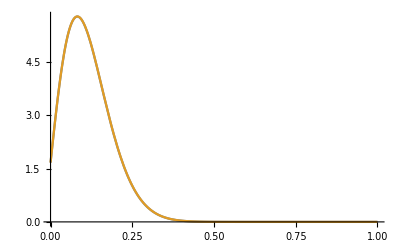

```mathematica
Plot[{Evaluate[haywardScenario4/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],
Evaluate[f[y,t] /.blah /. {t->time}]},{y, 0,1}]
```

```mathematica
statDist = 1/2 NIntegrate[Abs[Evaluate[haywardScenario4/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}] - Evaluate[{f[y, time]} /. blah]],{y,0,1}];
Print[statDist];
```

{{0.000483077}}

```mathematica
neutAUC = NIntegrate[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}], {y,0,1}]
pNeutFix = 1- neutAUC
```

0.984642

0.0153581

```mathematica
Integrate[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}],{y, start+Ψ,1}]
```

0.439281-5.66309 Ψ+18.1249 Ψ^2+103.368 Ψ^3-991.541 Ψ^4+2000.65 Ψ^5+10738.4 Ψ^6-80152.2 Ψ^7+196838. Ψ^8+92630.5 Ψ^9-2.19779×10^6 Ψ^10+7.39137×10^6 Ψ^11-1.12916×10^7 Ψ^12-4.27129×10^6 Ψ^13+6.76178×10^7 Ψ^14-1.81593×10^8 Ψ^15+2.64193×10^8 Ψ^16-1.33364×10^8 Ψ^17-3.77779×10^8 Ψ^18+1.19487×10^9 Ψ^19-1.86424×10^9 Ψ^20+1.73983×10^9 Ψ^21-4.77487×10^8 Ψ^22-1.54419×10^9 Ψ^23+3.31798×10^9 Ψ^24-3.84834×10^9 Ψ^25+2.84903×10^9 Ψ^26-9.2206×10^8 Ψ^27-9.04526×10^8 Ψ^28+1.8629×10^9 Ψ^29-1.82357×10^9 Ψ^30+1.17753×10^9 Ψ^31-4.45488×10^8 Ψ^32-4.22205×10^7 Ψ^33+2.24935×10^8 Ψ^34-2.07583×10^8 Ψ^35+1.2144×10^8 Ψ^36-4.69427×10^7 Ψ^37+7.18223×10^6 Ψ^38+5.80341×10^6 Ψ^39-6.268×10^6 Ψ^40+3.61917×10^6 Ψ^41-1.51861×10^6 Ψ^42+489356. Ψ^43-119825. Ψ^44+20693.9 Ψ^45-1873.82 Ψ^46-139.298 Ψ^47+74.8073 Ψ^48-10.7386 Ψ^49+0.611024 Ψ^50

```mathematica
tmp = Integrate[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}],{y, start+Ψ,1}]
```

0.439281-5.66309 Ψ+18.1249 Ψ^2+103.368 Ψ^3-991.541 Ψ^4+2000.65 Ψ^5+10738.4 Ψ^6-80152.2 Ψ^7+196838. Ψ^8+92630.5 Ψ^9-2.19779×10^6 Ψ^10+7.39137×10^6 Ψ^11-1.12916×10^7 Ψ^12-4.27129×10^6 Ψ^13+6.76178×10^7 Ψ^14-1.81593×10^8 Ψ^15+2.64193×10^8 Ψ^16-1.33364×10^8 Ψ^17-3.77779×10^8 Ψ^18+1.19487×10^9 Ψ^19-1.86424×10^9 Ψ^20+1.73983×10^9 Ψ^21-4.77487×10^8 Ψ^22-1.54419×10^9 Ψ^23+3.31798×10^9 Ψ^24-3.84834×10^9 Ψ^25+2.84903×10^9 Ψ^26-9.2206×10^8 Ψ^27-9.04526×10^8 Ψ^28+1.8629×10^9 Ψ^29-1.82357×10^9 Ψ^30+1.17753×10^9 Ψ^31-4.45488×10^8 Ψ^32-4.22205×10^7 Ψ^33+2.24935×10^8 Ψ^34-2.07583×10^8 Ψ^35+1.2144×10^8 Ψ^36-4.69427×10^7 Ψ^37+7.18223×10^6 Ψ^38+5.80341×10^6 Ψ^39-6.268×10^6 Ψ^40+3.61917×10^6 Ψ^41-1.51861×10^6 Ψ^42+489356. Ψ^43-119825. Ψ^44+20693.9 Ψ^45-1873.82 Ψ^46-139.298 Ψ^47+74.8073 Ψ^48-10.7386 Ψ^49+0.611024 Ψ^50

```mathematica
thresh = Solve[tmp == 1-sigCutoff && 0<Ψ<1, {Ψ}, Reals]
```

{{Ψ→0.192309}}

```mathematica
If[Length[thresh] != 1,Throw[{selectedNe,, " xxxx ", start,":"}]];
Ψ = Ψ /. thresh;
Ψ = Ψ[[1]];
Print[Ψ];
Print[pNeutFix +  NIntegrate[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}],{y, 0,start+Ψ}]];
pintAUC = NIntegrate[Evaluate[haywardScenario4/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],{y, 0,1}];
pintDetected = NIntegrate[Evaluate[haywardScenario4/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],{y, start+Ψ,1}];
Print[totalP, " xxxx ", Pdetected];
numAUC = NIntegrate[Evaluate[{f[y, time]} /. blah],{y,0,1}][[1]][[1]];
numDetected= NIntegrate[Evaluate[{f[y, time]} /. blah],{y,start + Ψ,1}][[1]][[1]];
Print["num:",numAUC, " xxxx ", numDetected];
Export[StringJoin["pDetection_","linked_VG",ToString[genVar],".csv"],{{selCoef,selectedNe,time, start,Ψ,pintAUC,pintDetected, numAUC, numDetected, statDist}}, "csv"]
```

0.192309

0.989995

totalP xxxx Pdetected

num:0.990573 xxxx 0.0196278

pDetection_linked_VG0.0568599.csv

```mathematica
(* genic *)
```

```mathematica
Clear[selCoef, genVar, blah, statDist];
Clear[neutAUC, pNeutFix,tmp,thresh,Ψ,blah,pintAUC,pintDetected,numAUC,numDetected,statDist];
selCoef = 10;
```

```mathematica
Get["genic-selection_1.m"];
```

```mathematica
For[k = 0, k ≤5,k++,
Josh[k] = Exp[γ  (y  - x)]* Sum[(-1/2)^j (γ)^(2j) * o[j], {j, 0, k}]
]
```

```mathematica
Clear[o]
```

```mathematica
Clear[fitVar, selectedNe, jumpSize, selCoef, genVar, start,time, soln];
start = 0.1;
time = 0.05;
```

```mathematica
blah = NDSolve[{D[f[y,t],t]== -γ D[y(1-y)f[y,t],y] + 1/2 D[y(1-y)f[y,t],{y,2}],
f[y,0]==Evaluate[PDF[TriangularDistribution[{(start - 0.001),(start + 0.001)},start],y]]} /. {γ->10},
f,{y,0,1},{t,0,0.25},MaxStepSize->.00025];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable y.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable y. Artificial boundary effects may be present in the solution.

```mathematica
neutral = Kimura[x,y,t,50];
Plot[{Evaluate[Josh[5]/.{x->start,t->time,γ->10}],
Evaluate[neutral /. {x->start,t->time}],
Evaluate[f[y,t] /.blah /. {t->time}]},
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2,
PlotLabels->{
"Genic",
"Neutral",
"Num"},
PlotRange->{{0,1},{-1,10}}]
```

-Graphics-

```mathematica
statDist = 1/2 NIntegrate[Abs[Evaluate[Josh[5]/.{x->start,t->time,γ->10}] - Evaluate[{f[y, time]} /. blah]],{y,0,1}];
Print[statDist];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0742032}. NIntegrate obtained 0.000022263 and 5.4911×10^-11 for the integral and error estimates.

{{0.0000111315}}

```mathematica
neutAUC = NIntegrate[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}], {y,0,1}];
pNeutFix = 1- neutAUC;
tmp = Integrate[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}],{y, start+Ψ,1}];
thresh = Solve[tmp == 1-sigCutoff && 0<Ψ<1, {Ψ}, Reals];
If[Length[thresh] != 1,Throw[{selectedNe,, " xxxx ", start,":"}]];
Ψ = Ψ /. thresh;
Ψ = Ψ[[1]];
Print[Ψ];
```

0.192309

```mathematica
Print[pNeutFix +  NIntegrate[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}],{y, 0,start+Ψ}]];
pintAUC = NIntegrate[Evaluate[Josh[5]/.{x->start,t->time,γ->10}],{y, 0,1}];
pintDetected = NIntegrate[Evaluate[Josh[5]/.{x->start,t->time,γ->10}],{y, start+Ψ,1}];
Print[totalP, " xxxx ", Pdetected];
numAUC = NIntegrate[Evaluate[{f[y, time]} /. blah],{y,0,1}][[1]][[1]];
numDetected= NIntegrate[Evaluate[{f[y, time]} /. blah],{y,start + Ψ,1}][[1]][[1]];
Print["num:",numAUC, " xxxx ", numDetected];
Export[StringJoin["pDetection_","genic",".csv"],{{selCoef,selectedNe,time, start,Ψ,pintAUC,pintDetected, numAUC, numDetected, statDist}}, "csv"]
```

0.989995

totalP xxxx Pdetected

num:0.994775 xxxx 0.0704205

pDetection_genic.csv